# Solovay-Kitaev Algorithm

## References

C. Dawson and M. Nielsen, Quantum Information and Computation 6, 81 (2006), “The Solovay-Kitaev algorithm”.

## BalancedCommutator

```mathematica
<<Q3`Solovay`
```

```mathematica
new=({{0.9689945920647197-0.18643612090113915 ⅈ, 0.15825427836029116+0.035307743526686745 ⅈ}, {-0.15825427836029105+0.035307743526662085 ⅈ, 0.9689945920646759+0.18643612090129802 ⅈ}})
```

{{0.968995-0.186436 ⅈ,0.158254+0.0353077 ⅈ},{-0.158254+0.0353077 ⅈ,0.968995+0.186436 ⅈ}}

```mathematica
MatrixForm/@({uu,vv}=BalancedCommutator[new])
GroupCommutator[uu,vv]-new//Chop//MatrixForm
```

RotationSystem::notuni: Matrix {{0.968995-0.186436 ⅈ,0.158254+0.0353077 ⅈ},{-0.158254+0.0353077 ⅈ,0.968995+0.186436 ⅈ}} is not a unitary matrix; its determinant is 1..

{(0.935676-0.267733 ⅈ | -0.0843935-0.213791 ⅈ
0.0843935-0.213791 ⅈ | 0.935676+0.267733 ⅈ),(0.935676-0.0576092 ⅈ | -0.293097+0.187844 ⅈ
0.293097+0.187844 ⅈ | 0.935676+0.0576092 ⅈ)}

(0 | 0
0 | 0)

```mathematica
MatrixForm/@BalancedCommutator[One[2]]
```

{(1 | 0
0 | 1),(1 | 0
0 | 1)}

```mathematica
Do[
mat=TheEulerRotation@RandomReal[{-1,1}Pi,3];
{V,W}=BalancedCommutator[mat];
gc=Chop@Chop@GroupCommutator[V,W];
Echo[mat-gc//Chop//MatrixForm],
10]
```

(0 | 0
0 | 0)

(0 | 0
0 | 0)

(0 | 0
0 | 0)

«7 more identical outputs»

This is one of the dangerous case.

```mathematica
mat={
{0.6176764285966168+0.19302865391947965 ⅈ,0.6924904732390966+0.31886158877364695 ⅈ},{-0.6924904732390966+0.31886158877364695 ⅈ,0.6176764285966168-0.19302865391947965 ⅈ}
};
mat//MatrixForm
```

(0.617676+0.193029 ⅈ | 0.69249+0.318862 ⅈ
-0.69249+0.318862 ⅈ | 0.617676-0.193029 ⅈ)

```mathematica
{V,W}=BalancedCommutator[mat];
gc=Chop@Chop@GroupCommutator[V,W];
mat-gc//Chop//MatrixForm
```

(0 | 0
0 | 0)

```mathematica
mat=TheRotation[2Pi/3,2];
mat//N//MatrixForm
{V,W}=BalancedCommutator[N@mat];
gc=Chop@Chop@GroupCommutator[V,W];
mat-gc//Chop//MatrixForm
```

(0.5 | -0.866025
0.866025 | 0.5)

(0 | 0
0 | 0)

## TheSolovay

```mathematica
<<Solovay`
```

```mathematica
MatrixForm/@TheSolovay@Range[0,7]
```

{(1 | 0
0 | 1),(1 | 0
0 | ⅇ^((ⅈ π)/4)),(1 | 0
0 | ⅈ),(1 | 0
0 | ⅇ^((3 ⅈ π)/4)),(1 | 0
0 | -1),(1 | 0
0 | ⅇ^(-(3 ⅈ π)/4)),(1 | 0
0 | -ⅈ),(1 | 0
0 | ⅇ^(-(ⅈ π)/4))}

```mathematica
MatrixForm@TheSolovay[9]
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

## SolovayChains

### Basic Examples

```mathematica
cc=SolovayChains[4]
```

{{4},{-2,9,-1},{-2,9,1},{2,9,-1},{2,9,1},{9,-3},{9,3},{9,-1,9,-1},{9,-1,9,1},{9,1,9,-1},{9,1,9,1},{-3,9},{3,9},{-1,9,-1,9},{-1,9,1,9},{1,9,-1,9},{1,9,1,9},{9,-2,9},{9,2,9}}

```mathematica
chainLength[ch_List]:=Total@Mod[Abs@ch,4,1]
```

```mathematica
chainLength/@cc
```

{4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}

```mathematica
mm=Dot@@@TheSolovay@cc//SimplifyThrough;
```

```mathematica
MatrixForm/@mm
```

{(1 | 0
0 | -1),(1/(√2) | 1/2-ⅈ/2
-ⅈ/(√2) | 1/2+ⅈ/2),(1/(√2) | 1/2+ⅈ/2
-ⅈ/(√2) | -1/2+ⅈ/2),(1/(√2) | 1/2-ⅈ/2
ⅈ/(√2) | -1/2-ⅈ/2),(1/(√2) | 1/2+ⅈ/2
ⅈ/(√2) | 1/2-ⅈ/2),(1/(√2) | -1/2-ⅈ/2
1/(√2) | 1/2+ⅈ/2),(1/(√2) | -1/2+ⅈ/2
1/(√2) | 1/2-ⅈ/2),(1/2 (1-(-1)^(3/4)) | -1/2 ⅈ (-1+(-1)^(1/4))
1/2 (1+(-1)^(3/4)) | -1/2 ⅈ (1+(-1)^(1/4))),(1/2 (1-(-1)^(3/4)) | 1/2 (-1+(-1)^(1/4))
1/2 (1+(-1)^(3/4)) | 1/2 (1+(-1)^(1/4))),(1/2 (1+(-1)^(1/4)) | 1/2 (-1-(-1)^(3/4))
1/2 (1-(-1)^(1/4)) | 1/2 (1-(-1)^(3/4))),(1/2 (1+(-1)^(1/4)) | 1/2 (-ⅈ+(-1)^(1/4))
1/2 (1-(-1)^(1/4)) | 1/2 (ⅈ+(-1)^(1/4))),(1/(√2) | 1/(√2)
-1/2-ⅈ/2 | 1/2+ⅈ/2),(1/(√2) | 1/(√2)
-1/2+ⅈ/2 | 1/2-ⅈ/2),(1/2 (1-(-1)^(3/4)) | 1/2 (1+(-1)^(3/4))
1/2 (ⅈ-(-1)^(3/4)) | 1/2 (-ⅈ-(-1)^(3/4))),(1/2 (1+(-1)^(1/4)) | 1/2 (1-(-1)^(1/4))
1/2 (-1-(-1)^(3/4)) | 1/2 (1-(-1)^(3/4))),(1/2 (1-(-1)^(3/4)) | 1/2 (1+(-1)^(3/4))
1/2 (-1+(-1)^(1/4)) | 1/2 (1+(-1)^(1/4))),(1/2 (1+(-1)^(1/4)) | 1/2 (1-(-1)^(1/4))
1/2 (-ⅈ+(-1)^(1/4)) | 1/2 (ⅈ+(-1)^(1/4))),(1/2-ⅈ/2 | 1/2+ⅈ/2
1/2+ⅈ/2 | 1/2-ⅈ/2),(1/2+ⅈ/2 | 1/2-ⅈ/2
1/2-ⅈ/2 | 1/2+ⅈ/2)}

### Demonstration of the SK Theorem

```mathematica
Quit[]
```

```mathematica
<<Solovay`
```

```mathematica
svyDictionary=Solovay`Private`svyDictionary;
```

```mathematica
chainLength[ch_List]:=Total@Mod[Abs@ch,4,1]
```

```mathematica
mat=TheRotation[Pi/4,1];
mat//MatrixForm
```

(Cos[π/8] | -ⅈ Sin[π/8]
-ⅈ Sin[π/8] | Cos[π/8])

```mathematica
EchoTiming[cc=svyDictionary[28];]
Length[cc]
```

141.207

858300

```mathematica
EchoTiming[ee=Sort@Map[Norm[#-mat]&,Values@cc];]
ListLogLogPlot[ee,PlotRange->All,Joined->True]
```

8.5382

-Graphics-

```mathematica
ee[[;;10]]
```

{0.0229649,0.0229649,0.0229649,0.0229649,0.0229649,0.0229649,0.0229649,0.0229649,0.0229649,0.0229649}

```mathematica
min=MinimalBy[cc,Norm[#-mat]&];
KeyGroupBy[min,chainLength]
```

<|24→<|{-1,9,1,9,-1,9,-1,9,1,9,1,9,-1,9,-1,9,1,9,1,9,1,9,-1,9}→{{0.916053-0.00444174 ⅈ,-0.0107233-0.400888 ⅈ},{0.0107233-0.400888 ⅈ,0.916053+0.00444174 ⅈ}}|>,28→<|{-1,9,1,9,1,9,1,9,-1,9,-1,9,1,9,1,9,-1,9,-1,9,1,9,-1,9,-1,9,1,9}→{{0.923636-0.0138641 ⅈ,-0.0183058-0.382583 ⅈ},{0.0183058-0.382583 ⅈ,0.923636+0.0138641 ⅈ}}|>|>

```mathematica
data={
{-Log@0.200389,12},
{-Log@0.130161,18},
{-Log@0.0229649,22},
{-Log@0.0229649,24}
}
```

{{1.60749,12},{2.03898,18},{3.77379,22},{3.77379,24}}

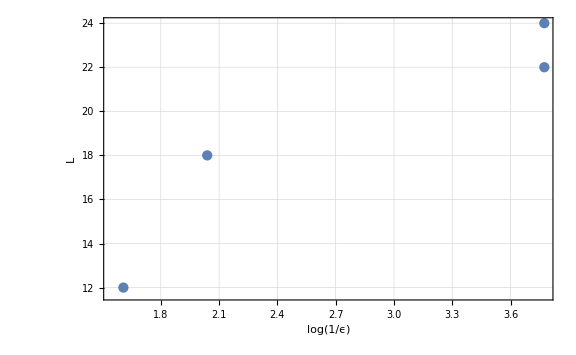

```mathematica
ListPlot[data,FrameLabel->{Log[1/ϵ],"L"}]
```

## SolovayKitaev

```mathematica
Quit[]
```

```mathematica
<<Solovay`
```

```mathematica
in=TheRotation[Pi/4,2];
in//MatrixForm
```

(Cos[π/8] | -Sin[π/8]
Sin[π/8] | Cos[π/8])

```mathematica
SolovayKitaev[in,0]
```

1.59724

{{9,-1,9,1,9,1,9,-1,9,1,9,-1,9,-1,9,1},{{0.875+0.0517767 ⅈ,-0.478553-0.0517767 ⅈ},{0.478553-0.0517767 ⅈ,0.875-0.0517767 ⅈ}}}

```mathematica
EchoTiming[{chain,out}=SolovayKitaev[in,2];]
```

0.614058

```mathematica
tmp=Dot@@N[TheSolovay@chain];
tmp//MatrixForm
```

(0.917143+0.000483136 ⅈ | -0.398558-0.000485667 ⅈ
0.398558-0.000485667 ⅈ | 0.917143-0.000483136 ⅈ)

```mathematica
tmp-out//Chop//MatrixForm
```

(0 | 0
0 | 0)

## Algorithm Demonstration

```mathematica
Quit[]
```

```mathematica
<<Solovay`
```

```mathematica
in=TheRotation[Pi/4,2];
in//MatrixForm
```

(Cos[π/8] | -Sin[π/8]
Sin[π/8] | Cos[π/8])

```mathematica
SolovayKitaev[in,0]
```

1.60032

{{9,-1,9,1,9,1,9,-1,9,1,9,-1,9,-1,9,1},{{0.875+0.0517767 ⅈ,-0.478553-0.0517767 ⅈ},{0.478553-0.0517767 ⅈ,0.875-0.0517767 ⅈ}}}

```mathematica
EchoTiming[{chain,out}=SolovayKitaev[in,2];]
```

0.614058

```mathematica
tmp=Dot@@N[TheSolovay@chain];
tmp//MatrixForm
```

(0.917143+0.000483136 ⅈ | -0.398558-0.000485667 ⅈ
0.398558-0.000485667 ⅈ | 0.917143-0.000483136 ⅈ)

```mathematica
tmp-out//Chop//MatrixForm
```

(0 | 0
0 | 0)

```mathematica
EchoTiming[mm=TheSolovay@chain;]
```

0.049336

```mathematica
Dimensions[mm]
```

{9898,2,2}

```mathematica
Block[
{$IterationLimit=Infinity},
EchoTiming[out=Dot@@N[TheSolovay@chain];]
]
```

0.655301

```mathematica
out//MatrixForm
```

(0.92388+0.000018595 ⅈ | -0.382681-0.0000791537 ⅈ
0.382681-0.0000791537 ⅈ | 0.92388-0.000018595 ⅈ)

```mathematica
Norm[in-out]
```

0.0000813475

```mathematica
Clear[svyMatrix];
svyMatrix[ch_List]:=Dot@@@N[TheSolovay@ch]/;Length[ch]<=$IterationLimit
svyMatrix[ch_List]:=Module[
{len=Length[ch],
n,r,cc},
{n,r}=QuotientRemainder[len,$IterationLimit];
cc=TakeList[ch,Append[Table[$IterationLimit,n],r]];
Apply[Dot,Dot@@@N[TheSolovay@cc]]
]
```

```mathematica
svyMatrix[Table[1,2^15+2]]
```

SparseArray[…]

```mathematica
Log[2,4096*4096*4096]
```

36